```mathematica
a=ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codes/alldata"]];
plot=ListLogLogPlot[a]
```

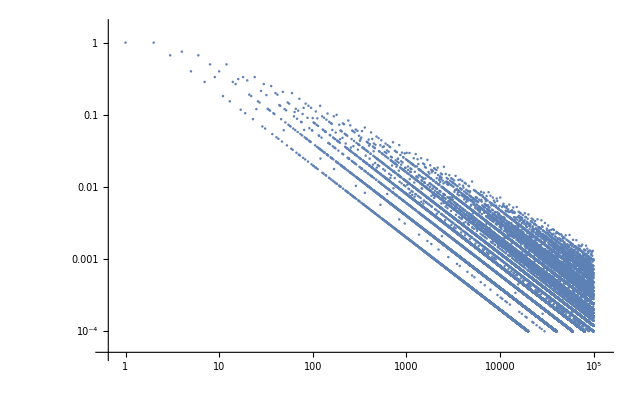

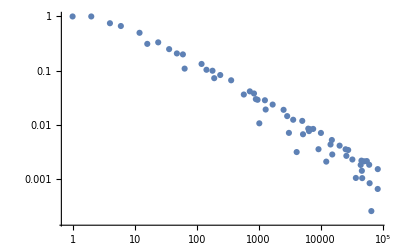

```mathematica
k=ListLogLogPlot[ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codes/toprow"]]]
```

```mathematica
b=ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codes/toprow"]];
refg = NonlinearModelFit[b,1/x^n,{n},x]
```

FittedModel[1/x^0.391579]

```mathematica
Manipulate[Show[ListLogLogPlot[b],LogLogPlot[x^j*k,{x,1,10^5}],Frame->True],{j,-1,1},{k,1,10}]
```

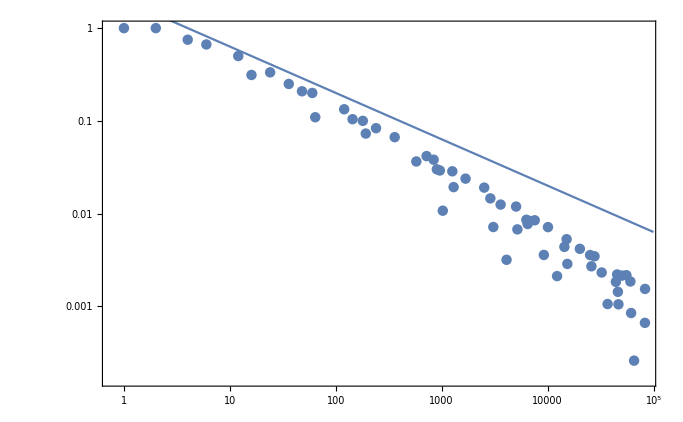

```mathematica
Show[ListLogLogPlot[b],LogLogPlot[(*x^(-2/3)*3*)(2 √x)/x,{x,1,10^5}],Frame->True]
```

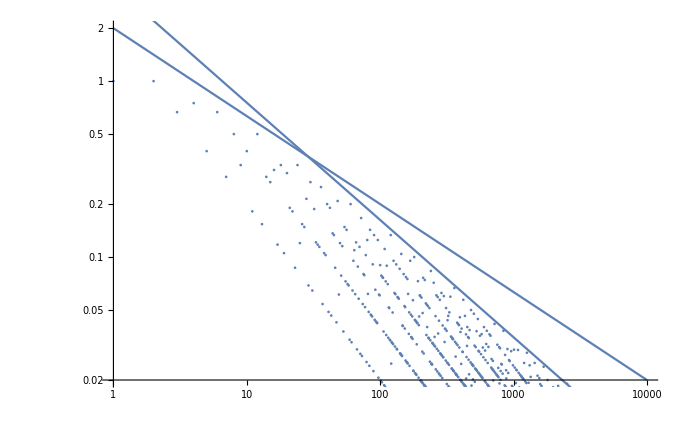

```mathematica
Show[LogLogPlot[(2Sqrt[x])/x,{x,1,10000}],LogLogPlot[(3.5 x^(1/3))/x,{x,1,100000}],ListLogLogPlot[Table[DivisorSigma[0,n]/n,{n,1,10000}]],Label->True]
```

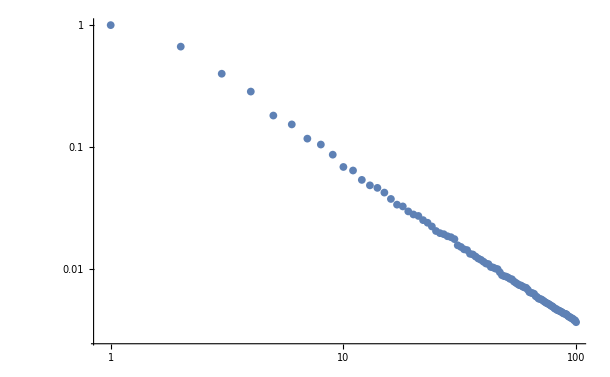

```mathematica
ListLogLogPlot[Table[DivisorSigma[0,n]/n,{n,Table[Prime[n],{n,1,100}]}]]
```

```mathematica
Show[Plot[3.5 x^(1/3),{x,1,10000}],ListPlot[Table[DivisorSigma[0,x],{x,1,10000}]]]
```

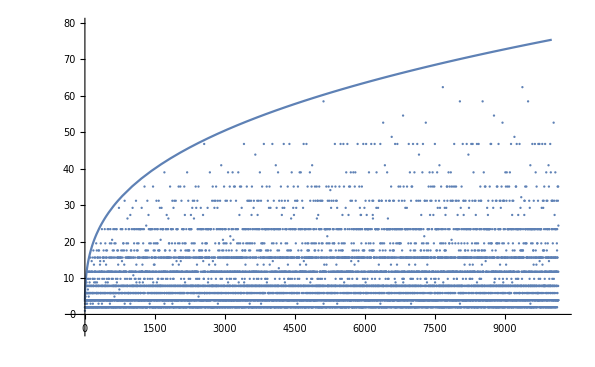

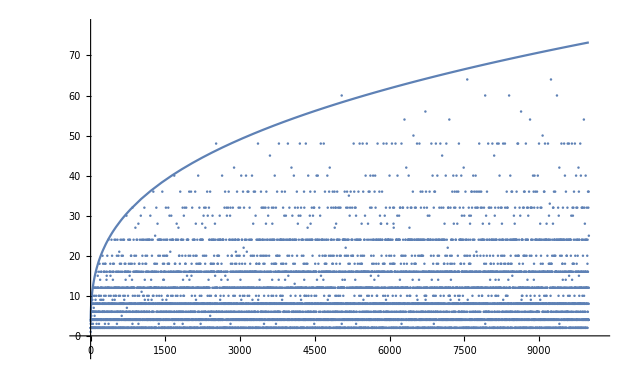

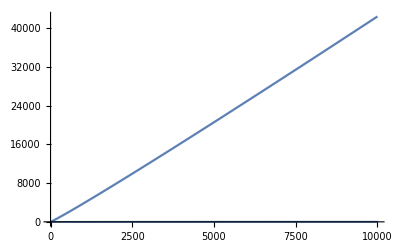

```mathematica
Show[Plot[E^EulerGamma x Log[Log[x]]+(0.65x)/Log[Log[x]],{x,1,10000}],ListPlot[Table[DivisorSigma[0,x],{x,1,10000}]]]
```

```mathematica
Limit[(∑_(k=1)^n k^(1/3)/DivisorSigma[0,k])/n,n->10]//N
```

NSum::nslim: Limit of summation n is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

0.687792

```mathematica
sigm[x_]:=DivisorSigma[0,x];
```

```mathematica
Limit[Sum[Max[Table[sigm[x], {x, 1, n}]]/n^(1/3), {n, 1, j}]/j, j -> 10]
```

Table::iterb: Iterator {x,1,n} does not have appropriate bounds.

lim_(j→10) (∑_(n=1)^j Table[sig[x],{x,1,n}]/n^(1/3))/j

```mathematica
Max[Table[sig[x],{x,1,4}]]
```

3

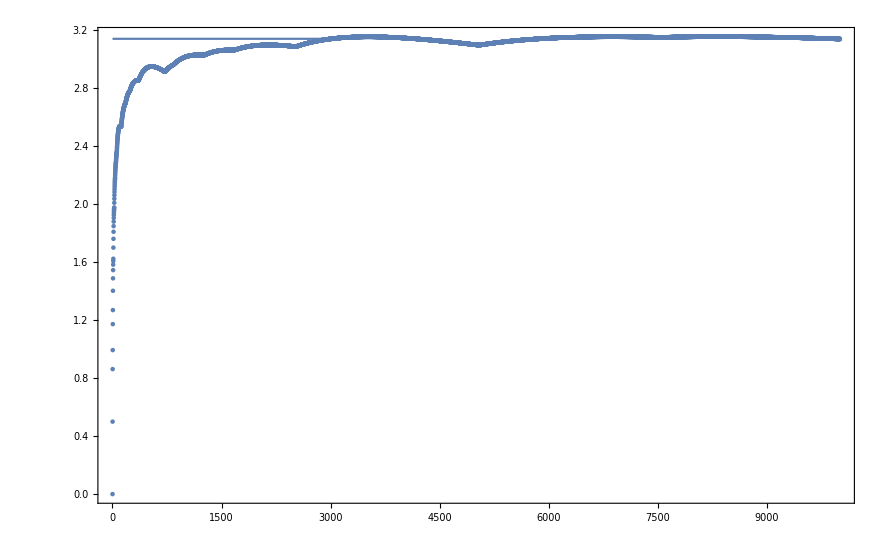

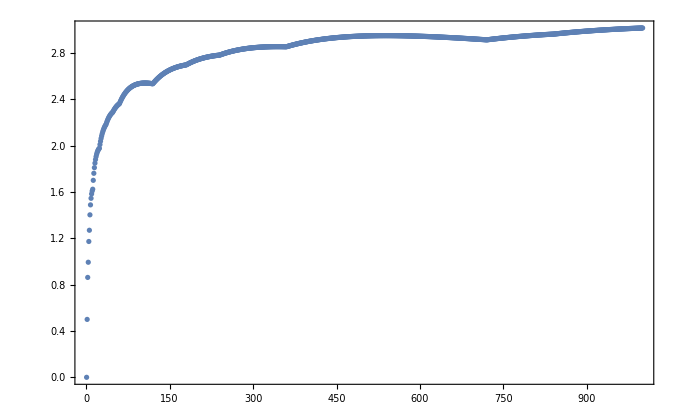

```mathematica
j=ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codesrm/testfile"]];
jplot=ListPlot[j];
Show[jplot,Plot[π,{x,1,3000}],Frame->True]
```